## zu 2.11 Veranschaulichung und Grenzwerte von Folgen

Zunächst die Befehlssyntax:

```mathematica
?DiscretePlot
```

DiscretePlot[expr,{n,n_max}] generates a plot of the values of expr when n runs from 1 to n_max.
DiscretePlot[expr,{n,n_min,n_max}] generates a plot of the values of expr when n runs from n_min to n_max.
DiscretePlot[expr,{n,n_min,n_max,dn}] uses steps dn. 
DiscretePlot[expr,{n,{n_1,n_2,…}}] uses the successive values n_1, n_2, ….
DiscretePlot[{expr_1,expr_2,…},…] plots the values of all the expr_i.

```mathematica
?Limit
```

Limit[expr,x->x_0] finds the limiting value of expr when x approaches x_0.

Die Folgen aus 2.11 (ii) - (v)

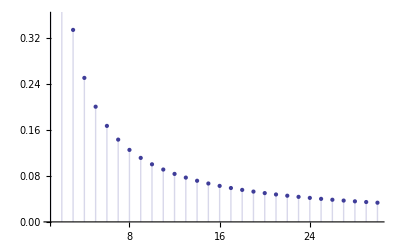

```mathematica
DiscretePlot[1/n,{n,1,30}]
```

```mathematica
Limit[1/n,n->Infinity]
```

0

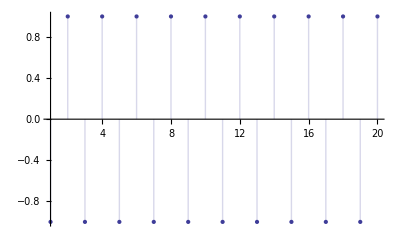

ⅇ^(2 ⅈ Interval[{0,π}])

```mathematica
DiscretePlot[(-1)^n,{n,1,20}]
Limit[(-1)^n,n->Infinity]
```

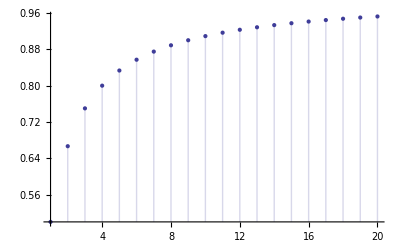

1

```mathematica
a[n_]:=n/(n+1)
DiscretePlot[a[n],{n,1,20}]
Limit[a[n],n->Infinity]
```

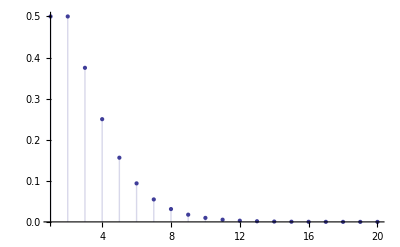

b/(1+b)

```mathematica
b[n_]:=n/2^n
DiscretePlot[b[n],{n,1,20}]
Limit[a[b],n->Infinity]
```